## Illustrative Examples to show how the Code works by using our 10-Store Test-Set

```mathematica
SetDirectory[NotebookDirectory[]]
<<ModList.m
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/Daten_MasterProject

```mathematica
coords=Import["TravelTim1_test.dat"];
StoreLabels=Map[Subscript["S",ToString[#]]&,Table[i,{i,0,Length[coords]-1}]]
StoreLabels=Prepend[Drop[StoreLabels,1],""]
coordsLabel=MapThread[Callout[#1,#2,Below]&,{coords,StoreLabels}]
```

{S_0,S_1,S_2,S_3,S_4,S_5,S_6,S_7,S_8,S_9,S_10}

{,S_1,S_2,S_3,S_4,S_5,S_6,S_7,S_8,S_9,S_10}

{Callout[{12602,5915},,Below],Callout[{11746,11976},S_1,Below],Callout[{13674,2963},S_2,Below],Callout[{5028,11523},S_3,Below],Callout[{4166,8309},S_4,Below],Callout[{7160,9433},S_5,Below],Callout[{5471,7701},S_6,Below],Callout[{14283,13742},S_7,Below],Callout[{9535,10759},S_8,Below],Callout[{2124,9104},S_9,Below],Callout[{244,3643},S_10,Below]}

```mathematica
?Take2
?TakeSubList
```

```mathematica
ServiceTimes=Import["StoreServiceTimes_Test_Mathematica.csv","CSV"];
ServiceTimes=Drop[ServiceTimes,1]
```

{{STO_011,Mo-Sa,18:00,23:00},{STO_002,Mo-Sa,06:30,22:00},{STO_003,Mo-Sa,06:15,22:00},{STO_004,Mo-Sa,06:00,22:00},{STO_005,Mo-Sa,06:00,00:00},{STO_006,Mo-Sa,06:00,22:00},{STO_007,Mo-Sa,06:00,22:00},{STO_008,Mo-Sa,06:00,22:00},{STO_009,Mo-Sa,20:00,00:00},{STO_010,Mo-Sa,20:00,00:00}}

```mathematica
ServiceTimes=Flatten[Transpose[{Drop[StoreLabels,1],TakeSubList[ServiceTimes,3,4]}],0]
```

{{S_1,{18:00,23:00}},{S_2,{06:30,22:00}},{S_3,{06:15,22:00}},{S_4,{06:00,22:00}},{S_5,{06:00,00:00}},{S_6,{06:00,22:00}},{S_7,{06:00,22:00}},{S_8,{06:00,22:00}},{S_9,{20:00,00:00}},{S_10,{20:00,00:00}}}

```mathematica
Map[{#1,ToString[#2]}&,ServiceTimes]
```

Function::slotn: Slot number 2 in {#1,ToString[#2]}& cannot be filled from ({#1,ToString[#2]}&)[{S_2,{18:00,23:00}}].

Function::slotn: Slot number 2 in {#1,ToString[#2]}& cannot be filled from ({#1,ToString[#2]}&)[{S_3,{06:30,22:00}}].

Function::slotn: Slot number 2 in {#1,ToString[#2]}& cannot be filled from ({#1,ToString[#2]}&)[{S_4,{06:15,22:00}}].

General::stop: Further output of Function::slotn will be suppressed during this calculation.

{{{S_2,{18:00,23:00}},#2},{{S_3,{06:30,22:00}},#2},{{S_4,{06:15,22:00}},#2},{{S_5,{06:00,22:00}},#2},{{S_6,{06:00,00:00}},#2},{{S_7,{06:00,22:00}},#2},{{S_8,{06:00,22:00}},#2},{{S_9,{06:00,22:00}},#2},{{S_10,{20:00,00:00}},#2},{{S_11,{20:00,00:00}},#2}}

```mathematica
OpeningHours=Style[TableForm[ServiceTimes,TableHeadings->{None,{"Store","Service Time"}}],{15,Black}]
```

Store | Service Time
S_1 | 18:00
23:00
S_2 | 06:30
22:00
S_3 | 06:15
22:00
S_4 | 06:00
22:00
S_5 | 06:00
00:00
S_6 | 06:00
22:00
S_7 | 06:00
22:00
S_8 | 06:00
22:00
S_9 | 20:00
00:00
S_10 | 20:00
00:00

```mathematica
graph=ListPlot[{coordsLabel,{Callout[{12602,5915},"Hub",Below]}},
Frame->True,
LabelStyle->{30,Black},
FrameLabel->{{"y / a.u.",None},{"x / a.u.",None}},
LabelStyle->25,
PlotStyle->{{PointSize[0.02],Blue},{PointSize[0.07],Red}},
PlotTheme->{"Classic","Detailed"},
ImageSize->1000,
PlotLegends->Placed[{"Stores 1-10","Hub"},Top]]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["Graph_xy.pdf",graph]
```

/home/lindorfer/ReWiTech/Masterarbeit/Programs/Daten_MasterProject

Graph_xy.pdf

```mathematica
coords
```

{{12602,5915},{11746,11976},{13674,2963},{5028,11523},{4166,8309},{7160,9433},{5471,7701},{14283,13742},{9535,10759},{2124,9104},{244,3643}}

```mathematica
pathInitial={1,11,10,1,10,5,1,4,1,5,1,5,7,1,8,2,1,7,6,1,6,9,2,1,2,3,1,2,1};
```

```mathematica
path=pathInitial
```

{1,11,10,1,10,5,1,4,1,5,1,5,7,1,8,2,1,7,6,1,6,9,2,1,2,3,1,2,1}

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

```mathematica
For[i = 1, i ≤ Length[path]-1,i++,
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]]
]
```

```mathematica
arrowlist
```

{Arrowheads[0.015],RGBColor[0.7469371536801328, 0.5166777048083995, 0.010702255593669552],Arrow[{{12602,5915},{244,3643}}],Arrow[{{244,3643},{2124,9104}}],Arrow[{{2124,9104},{12602,5915}}],RGBColor[0.7929494316446319, 0.7636501420741333, 0.2881344352011217],Arrow[{{12602,5915},{2124,9104}}],Arrow[{{2124,9104},{4166,8309}}],Arrow[{{4166,8309},{12602,5915}}],RGBColor[0.14564575978356697, 0.5829296215450954, 0.8994813163383562],Arrow[{{12602,5915},{5028,11523}}],Arrow[{{5028,11523},{12602,5915}}],RGBColor[0.033498498029185475, 0.14177931851322167, 0.7481425203852512],Arrow[{{12602,5915},{4166,8309}}],Arrow[{{4166,8309},{12602,5915}}],RGBColor[0.5869757890377281, 0.3926349923771897, 0.888121357105413],Arrow[{{12602,5915},{4166,8309}}],Arrow[{{4166,8309},{5471,7701}}],Arrow[{{5471,7701},{12602,5915}}],RGBColor[0.908597170089577, 0.3334314226454964, 0.48420488930646965],Arrow[{{12602,5915},{14283,13742}}],Arrow[{{14283,13742},{11746,11976}}],Arrow[{{11746,11976},{12602,5915}}],RGBColor[0.7275664532625199, 0.8209831571447663, 0.4170994380950299],Arrow[{{12602,5915},{5471,7701}}],Arrow[{{5471,7701},{7160,9433}}],Arrow[{{7160,9433},{12602,5915}}],RGBColor[0.01270049692235009, 0.9633748768992065, 0.859787493765505],Arrow[{{12602,5915},{7160,9433}}],Arrow[{{7160,9433},{9535,10759}}],Arrow[{{9535,10759},{11746,11976}}],Arrow[{{11746,11976},{12602,5915}}],RGBColor[0.7999917864282142, 0.4972449145639435, 0.20026357495185665],Arrow[{{12602,5915},{11746,11976}}],Arrow[{{11746,11976},{13674,2963}}],Arrow[{{13674,2963},{12602,5915}}],RGBColor[0.27068831367362534, 0.7071717398448931, 0.2670505820609872],Arrow[{{12602,5915},{11746,11976}}],Arrow[{{11746,11976},{12602,5915}}]}

```mathematica
Show[graph,Graphics[arrowlist]]
```

-Graphics-

```mathematica
pathFinal={1,5,1,4,1,5,1,6,1,2,9,1,8,1,6,10,1,7,1,3,1,11,1};
```

```mathematica
path=pathFinal
```

{1,5,1,4,1,5,1,6,1,2,9,1,8,1,6,10,1,7,1,3,1,11,1}

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

```mathematica
Show[graph,Graphics[arrowlist]]
```

-Graphics-

### Capacity = 50

```mathematica
pathcap50init={1,11,10,5,1,4,6,1,5,7,1,8,2,9,6,7,1,7,3,1};
pathcap50final={1,11,10,1,4,7,1,6,3,1,8,2,9,1,5,1};
```

```mathematica
path=pathcap50init
```

{1,11,10,5,1,4,6,1,5,7,1,8,2,9,6,7,1,7,3,1}

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

```mathematica
Show[graph,Graphics[arrowlist]]
```

-Graphics-

```mathematica
path=pathcap50final
```

{1,11,10,1,4,7,1,6,3,1,8,2,9,1,5,1}

```mathematica
arrowlist={Arrowheads[0.015]};
For[i = 1, i ≤ Length[path]-1,i++,
If[path[[i]] == 1,
AppendTo[arrowlist,RGBColor[RandomReal[1],RandomReal[1],RandomReal[1]]],];
AppendTo[arrowlist,Arrow[{coords[[path[[i]]]],coords[[path[[i+1]]]]}]];
]
```

```mathematica
Show[graph,Graphics[arrowlist]]
```

-Graphics-

```mathematica
scoreinitial=136841;
scorefinal=128225;
```

```mathematica
Illustrative Examples for Dock-Schedueling to show how the Code works by using our 10-Store Test-Set
```

```mathematica
dock0={{0,2400,0},{33631,36031,1},{36031,38251,0},{46751,48911,0},{52689,54729,2},{57279,59559,1},{67081,69181,0}};
dock1={{0,2340,1},{2340,4620,2},{34929,37329,2}};
```

```mathematica
truck0={{0,35169,0,0},{36031,46751,8,0},{46751,67081,5,0},{67081,94359,6,0}};
truck1={{0,33631,7,1},{33631,57279,1,0},{57279,80973,4,0}};
truck2={{2340,34929,2,1},{34929,52689,3,1},{52689,81899,9,0}};
```

```mathematica
docksfinal={{0,12270,Style[Labeled[2400,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[2400,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],18099,Style[Labeled[2220,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],0,Style[Labeled[2340,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],6160,Style[Labeled[2280,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],7985,Style[Labeled[2040,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],2423,Style[Labeled[2100,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]]},{0,12146,Style[Labeled[2400,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],21278,Style[Labeled[2160,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],30003,Style[Labeled[2280,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]}};
```

```mathematica
docksinitial={{Style[Labeled[2400,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],31231,Style[Labeled[2400,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[2220,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],8500,Style[Labeled[2160,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]],3778,Style[Labeled[2040,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],2550,Style[Labeled[2280,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],7522,Style[Labeled[2100,Style["Truck 1",Black,12],Center],ColorData["BrightBands",0]]},{Style[Labeled[2340,Style["Truck 2",Black,12],Center],ColorData["BrightBands",0.1]],0,Style[Labeled[2280,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]],30309,Style[Labeled[2400,Style["Truck 3",Black,12],Center],ColorData["BrightBands",0.2]]}};
```

```mathematica
color={};
For[i = 1, i< 15,i++,
AppendTo[color,Red];
AppendTo[color,White];
]
```

```mathematica
color
```

{RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1],RGBColor[1, 0, 0],GrayLevel[1]}

```mathematica
lblStyle=Style[#,22,Black]&;
lblStyle/@{"Dock 1","Dock 2","Dock 3","Dock 4","Dock 5"}
```

{Dock 1,Dock 2,Dock 3,Dock 4,Dock 5}

```mathematica
PlotBarChart[list_,max_,ndocks_:5,imgsize_:700,linestart_:0.34,color_:color,type_:"Dock",xrange_:All]:=BarChart[list,
ChartLayout->"Stacked",
ChartLabels->{lblStyle/@Table[type <>ToString[i],{i,1,ndocks}],None},
FrameLabel->{"","time / sec"},
LabelStyle->{22,Black,Italic},
ImageSize->imgsize,
Frame->True,
FrameStyle->Directive[Thickness[0.002]],
PlotTheme->"Detailed",
ChartStyle->color,
PlotRange->{xrange,{0,max}},
Epilog->{Black,{Thickness[0.01],Line[{{linestart,max},{100,max}}]}}
(*,ChartLegends->Placed[SwatchLegend[{Black},{"Latest Return-Time"},LegendMarkers->"Line",LegendMarkerSize->20],Top]*)
]
```

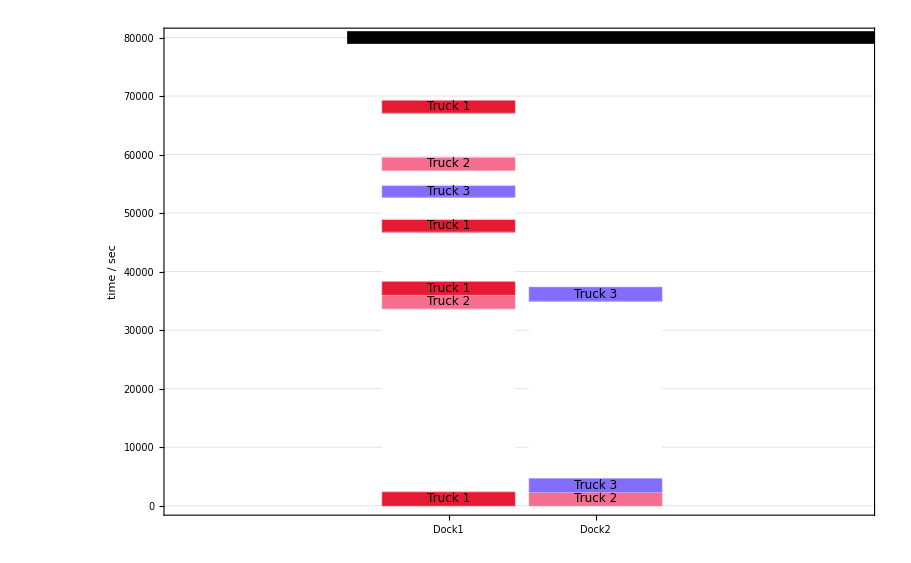

```mathematica
dinit=PlotBarChart[docksinitial,80000,2,900,0.31,color]
```

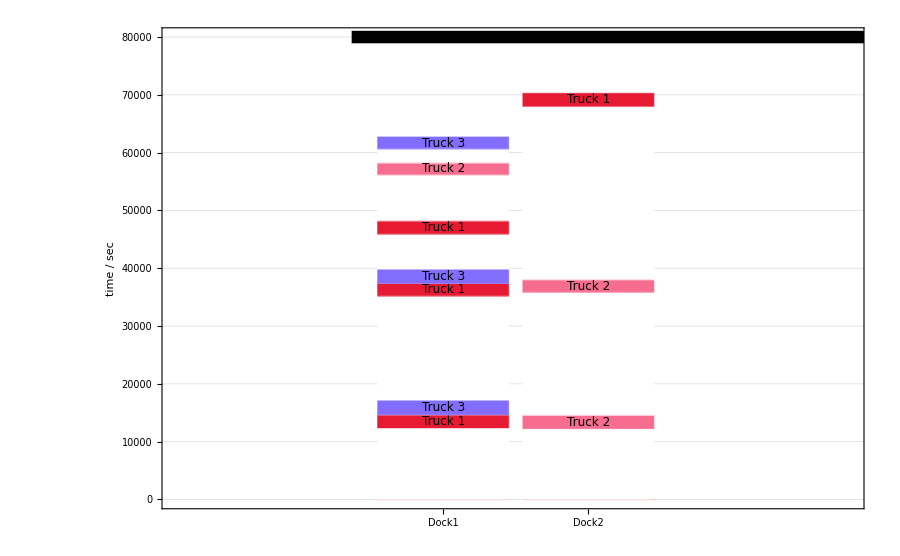

```mathematica
dfinal=PlotBarChart[docksfinal,80000,2,900,0.37,color]
```

```mathematica
trucksfinal={{0,12270,Style[Labeled[22899,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],0,Style[Labeled[10720,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],0,Style[Labeled[22098,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],0,Style[Labeled[19537,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]]},{0,12146,Style[Labeled[23678,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[20330,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[29210,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]]},{0,14670,Style[Labeled[18210,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],4509,Style[Labeled[19382,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],3846,Style[Labeled[27278,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]}};

trucksinitial={{Style[Labeled[35169,Style["Job 0",Black,12],Center],Lighter[ColorData["Rainbow",0]]],862,Style[Labeled[10720,Style["Job 8",Black,12],Center],Lighter[ColorData["Rainbow",0.8]]],0,Style[Labeled[20330,Style["Job 5",Black,12],Center],Lighter[ColorData["Rainbow",0.5]]],0,Style[Labeled[27278,Style["Job 6",Black,12],Center],Lighter[ColorData["Rainbow",0.6]]]},{Style[Labeled[33631,Style["Job 7",Black,12],Center],Lighter[ColorData["Rainbow",0.7]]],0,Style[Labeled[23648,Style["Job 1",Black,12],Center],Lighter[ColorData["Rainbow",0.1]]],0,Style[Labeled[23694,Style["Job 4",Black,12],Center],Lighter[ColorData["Rainbow",0.4]]]},{0,2340,Style[Labeled[32589,Style["Job 2",Black,12],Center],Lighter[ColorData["Rainbow",0.2]]],0,Style[Labeled[17760,Style["Job 3",Black,12],Center],Lighter[ColorData["Rainbow",0.3]]],0,Style[Labeled[29210,Style["Job 9",Black,12],Center],Lighter[ColorData["Rainbow",0.9]]]}};
```

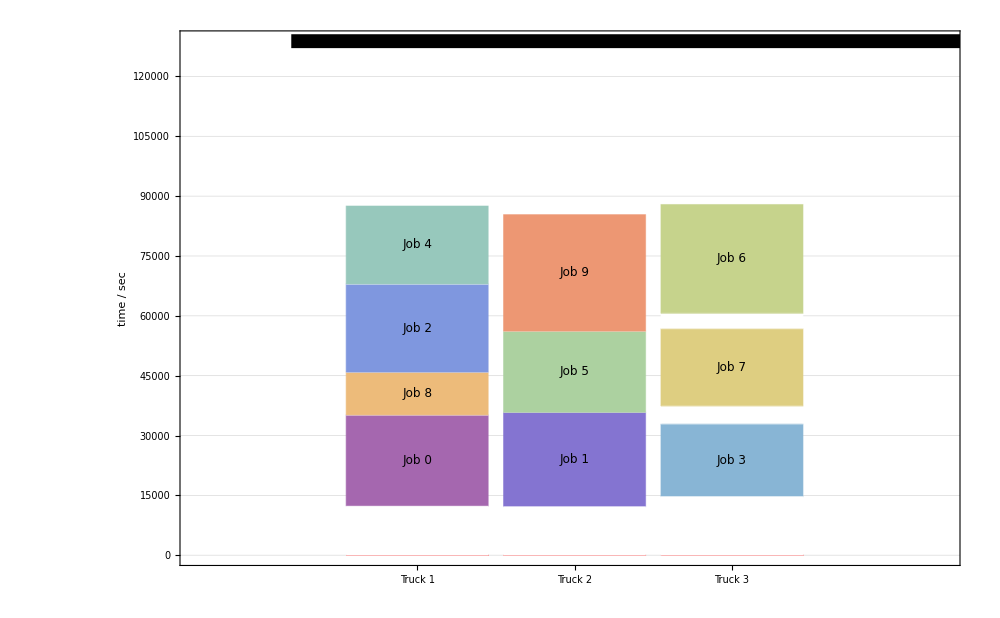

```mathematica
PlotBarChart[trucksfinal,128842,10,1000,0.2,color, "Truck "]
```

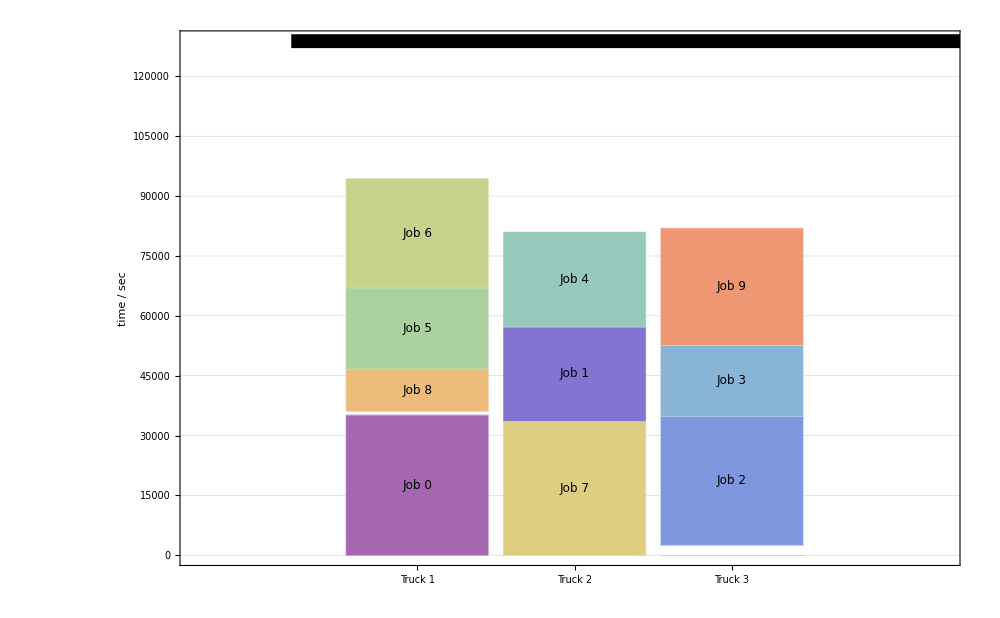

```mathematica
PlotBarChart[trucksinitial,128842,10,1000,0.2,color, "Truck "]
```